# Introduction to SPQR

SPQR is a package for performing multivariate polynomial and rational function division, as well as related functionality. Inspired by recent developments in the Integration by Parts (IBP) scattering amplitudes subfield, the polynomial division is performed by building and subsequently row reducing linear systems.

The row reduction is performed by sampling and reconstructing over finite fields, which is handled by the external package FiniteFlow. In this tutorial we outline the core functionality of the package, as well as showcase various examples and applications. For all details and options for every function, see the guide page SPQR.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

table showcase and options something here also

Loading the Package

```mathematica
Get["SPQR`"]
```

## Polynomial Division

### A first example

We begin by setting up a polynomial division problem

We define a list of target polynomials we want to reduce, as well as an ideal (list of polynomials) we would like to reduce against

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

This ideal depends on two variables, and two parameters

```mathematica
ideal // Variables
Complement[%,variables]
```

{a,x,y}

{a}

We now build a system of equations and load them into FiniteFlow using BuildPolynomialSystem. We discuss the workings of this function in the next section

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight];
```

The generated graph can be seen with

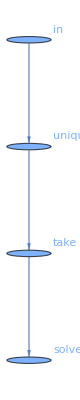

```mathematica
system // First // FFGraphDraw
```

We can now use FiniteFlow to reconstruct the output of the polynomial reduction with ReconstructPolynomialRemainder

```mathematica
results=ReconstructPolynomialRemainder[system]
```

Generated 18 sample points

Approximate time per evaluation (single core): 2.2e-05 sec.

{(1/2+(9 a)/2+3 a^2+(49 a^3)/16+a^3 b^2)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2,7/2+s-(3 y)/2+y^2/2,9/4-(3 a)/16+(-3+(31 a)/16+a^2/32) y+(9/2-(75 a)/16-(3 a^2)/16) y^2+(-3/4+(95 a)/16+(11 a^2)/32) y^3+(-(45 a)/16-(3 a^2)/16) y^4+((7 a)/16+a^2/32) y^5}

We can check this result against Mathematica's built in functions GroebnerBasis and PolynomialReduce

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions];
ansGB = PolynomialReduce[targets,gb,variables] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

Note how we never needed an explicit Groebner Basis in the computation using SPQR. Only the output of the polynomial division is reconstructed. This is different to Mathematica, where if we don't build a Groebner Basis, the result of the polynomial reduction will not be well defined

```mathematica
ansNoGB = PolynomialReduce[targets,ideal,variables] // Map[Last] // Factor
ansNoGB - results // Factor // ContainsOnly[{0}]
```

{1/(4 a^3)(108-9 a+12 a^3+4 a^3 b^2+72 x+54 a x-120 x^2-36 a x^2-48 x^3-24 a x^3+32 x^4+16 a x^4+54 a y+2 a^3 y-90 a y^2+18 a^2 y^2-6 a^3 y^2+27 a y^3-54 a^2 y^3+2 a^3 y^3+18 a^2 y^4),1/2 (7+2 s-3 y+y^2),x^3}

False

### BuildPolynomialSystem in more detail

Let us examine the output of BuildPolynomialSystem in more detail

```mathematica
system
```

{ffGraph$965209474611466,{a,b,s,extraparam},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

system[[1]] is simply the name of the graph that has been built. system[[2]] is the list of parameters that is eventually reconstructed by FiniteFlow. In system[[3]], DepVars represents the list of the three target polynomials we are reducing.

IndepVars is the most important output, and represents the irreducible monomials that were found by the linear system during row reduction. These are completely analogous to the "master integrals" in an IBP reduction for Feynman integrals. They are indexed by the notation j[a,b] = x^a y^b

Specifically we have

```mathematica
"IndepVars" // ReplaceAll[system[[3]]]//ReplaceAll[j[x__]:>Times@@(variables^{x})]
```

{y^5,y^4,y^3,y^2,y,1}

How do we know if the monomials have been found are correct? We can verify using the command FindIrreducibleMonomials

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

These can be passed as an option to BuildPolynomialSystem, which will automatically check if the irreducible monomials found by row reduction agree

If the output is as before, then the check has been passed

```mathematica
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

{ffGraph$389974141915986,{a,b,s,extraparam},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

If we however consider a system with too small of a seed, then in exact analogy to IBPs, the system will not reduce fully

```mathematica
maxWeight = 7;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

Irreducible monomials do not match. Try increasing the system size

Found 7 monomials: {x^5 y^7,y^5,y^4,y^3,y^2,y,1}

$Failed

Whenever possible, it is always recommended to precompute the irreducible monomials and to pass them as an option to BuildPolynomialSystem, in order to always insure a correct reduction when reconstruction is performed

### Further Basic Examples

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder"

Define an ideal and a target polynomials to reduce

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{y^3,x^2,y^2,x,y,1}

Build the polynomial system and reconstruct the remainder

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials,"MonomialOrder"->DegreeReverseLexicographic]
```

{ffGraph$993856776204633,{a,b,s,extraparam},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,3],j[2,0],j[0,2],j[1,0],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

```mathematica
results=ReconstructPolynomialRemainder[system, "DeleteGraph" -> False]
```

Generated 0 sample points

Approximate time per evaluation (single core): 2.0449e-05 sec.

{(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4+a^4 b^2)/a^4+((-9-(9 a)/2-(9 a^2)/4) x)/a^3+((4+24 a+54 a^2+a^3/2) x^2)/a^4+((-18-18 a+(63 a^2)/4+a^3/2) y)/a^3+((24+3 a-(153 a^2)/4-(3 a^3)/2) y^2)/a^3+((-9/2+(9 a)/4+(99 a^2)/8+a^3/2) y^3)/a^3,7/2+s-(3 y)/2+y^2/2,15/8-(3 a)/16+(7/4+a/8) x-(3 x^2)/2+(1/2+(5 a)/8) y+(-3/4-(3 a)/8) y^2+(1/8+a/16) y^3}

Check against built in functions

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions,MonomialOrder->DegreeReverseLexicographic];
ansGB = PolynomialReduce[targets,gb,variables,MonomialOrder->DegreeReverseLexicographic] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

### Other options for ReconstructPolynomialRemainder

Here we showcase some other options for ReconstructPolynomialRemainder that might be useful to the user

```mathematica
ReconstructPolynomialRemainder // Options
```

{Vector→False,PrintDebugInfo→1,DeleteGraph→True}

Vector | False | return only the vector of coefficients of irreducible monomials
PrintDebugInfo | 1 | print intermediate information during rational reconstruction from FiniteFlow 
DeleteGraph | True | delete the FiniteFlow computational graph after reconstruction

By default, ReconstructPolynomialRemainder returns the polynomial remainder as a linear combination of irreducible monomials

```mathematica
ReconstructPolynomialRemainder[system, "DeleteGraph" -> False]
```

Generated 0 sample points

Approximate time per evaluation (single core): 1.9389e-05 sec.

{(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4+a^4 b^2)/a^4+((-9-(9 a)/2-(9 a^2)/4) x)/a^3+((4+24 a+54 a^2+a^3/2) x^2)/a^4+((-18-18 a+(63 a^2)/4+a^3/2) y)/a^3+((24+3 a-(153 a^2)/4-(3 a^3)/2) y^2)/a^3+((-9/2+(9 a)/4+(99 a^2)/8+a^3/2) y^3)/a^3,7/2+s-(3 y)/2+y^2/2,15/8-(3 a)/16+(7/4+a/8) x-(3 x^2)/2+(1/2+(5 a)/8) y+(-3/4-(3 a)/8) y^2+(1/8+a/16) y^3}

Internally only the list of coefficients in front of the irreducible monomials is stored. The "Vector" → True option makes the function return the list of coefficients directly

```mathematica
ReconstructPolynomialRemainder[system, "Vector" -> True, "DeleteGraph" -> False]
```

Generated 0 sample points

Approximate time per evaluation (single core): 1.8214e-05 sec.

{{(-9/2+(9 a)/4+(99 a^2)/8+a^3/2)/a^3,(4+24 a+54 a^2+a^3/2)/a^4,(24+3 a-(153 a^2)/4-(3 a^3)/2)/a^3,(-9-(9 a)/2-(9 a^2)/4)/a^3,(-18-18 a+(63 a^2)/4+a^3/2)/a^3,(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4+a^4 b^2)/a^4},{0,0,1/2,0,-3/2,7/2+s},{1/8+a/16,-3/2,-3/4-(3 a)/8,7/4+a/8,1/2+(5 a)/8,15/8-(3 a)/16}}

## Rational Function Division via Companion Matrices

### Polynomial Division with Companion Matrices

Companion matrices M_x are matrices we can generate from any variable in our system x→ M_x, which encode information on the structure of the ideal, and in particular its polynomial remainders. We delegate further mathematical discussion to manuscript accompanying this package, and here focus on the computational commands.

We define a (single) polynomial we want to reduce, as well as an ideal (list of polynomials) we would like to reduce against

```mathematica
variables = {x,y};
target = a*x^5*y^5*y^2+3+x*y^2;
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

Precomputing the irreducible monomials is mandatory for building companion matrices

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

We can then generate the companion matrices using BuildCompanionMatrices. A companion matrix is generated for each variable (not parameter) in the system, so in this case {x,y}

```mathematica
maxWeight = 4;
cmats = BuildCompanionMatrices[ideal,variables,maxWeight,irreducibleMonomials];
```

The output in the graph can be seen more clearly with

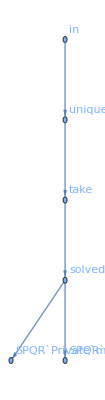

```mathematica
cmats // First // FFGraphDraw
```

The output cmats is very similar to the output produced by BuildPolynomialSystem. Indeed, BuildCompanionMatrices is essentially a wrapper function for BuildPolynomialSystem

```mathematica
cmats
```

{ffGraph$982776451458205,{a,extraparam},{DepVars→{targ[1],targ[2],targ[3],targ[4],targ[5],targ[6],targ[7],targ[8],targ[9],targ[10],targ[11],targ[12]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{SPQR`Private`m[cmatx],SPQR`Private`m[cmaty]},{x,y}}

Before proceeding it is important to mention that if the maxWeight is not large enough, the companion matrix generation will fail, as not all the required polynomials will have been reduced correctly

```mathematica
maxWeight = 3; 
BuildCompanionMatrices[ideal,variables,maxWeight,irreducibleMonomials];
```

Irreducible monomials do not match. Try increasing the system size

Found 8 monomials: {x y^5,y^6,y^5,y^4,y^3,y^2,y,1}

The next step in the procedure is to produce a companion matrix for the polynomial we want to reduce. This can be achieved with BuildTargetCompanionMatrix

```mathematica
targetcmat = BuildTargetCompanionMatrix[target,cmats]
```

{ffGraph$982776451458205,{a,extraparam},SPQR`Private`m[o$43],{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{x,y}}

This command will parse the expression given in Mathematica and will automatically construct the relevant graph in FiniteFlow

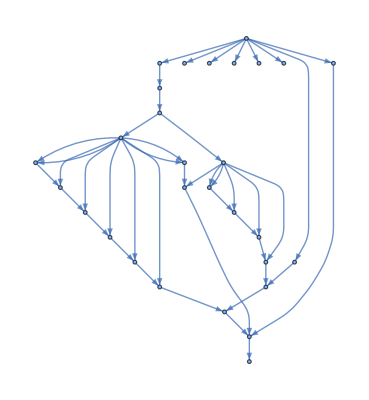

```mathematica
targetcmat // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally, we can extract the output of the polynomial division from the target companion matrix, with the command ReconstructTargetCompanionMatrix

```mathematica
result = ReconstructTargetCompanionMatrix[targetcmat,"DeleteGraph"->False]
```

Generated 6 sample points

Approximate time per evaluation (single core): 2.1e-05 sec.

(1/2+(9 a)/2+3 a^2+(49 a^3)/16)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2

We can check this result against Mathematica

```mathematica
gb = GroebnerBasis[ideal,variables];
gbAns=PolynomialReduce[target,gb,variables]//Last
result - gbAns // Factor // Equal[#,0]& // TrueQ
```

(8+72 a+48 a^2+49 a^3)/(16 a^3)+((-48-468 a-342 a^2-7 a^3) y)/(16 a^3)+((40+576 a+576 a^2+41 a^3) y^2)/(16 a^3)+((-48-612 a-630 a^2-97 a^3) y^3)/(16 a^3)+((8+264 a+216 a^2+55 a^3) y^4)/(16 a^3)-(9 (4+2 a+a^2) y^5)/(16 a^2)

True

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder" to BuildCompanionMatrices , in a manner identical to BuildPolynomialSystem. Make sure to also pass the same option to FindIrreducibleMonomials!

### Rational Function Division with Companion Matrices

Companion matrices allow us to also construct the polynomial remainder with respect to rational functions, not just polynomials. The procedure is identical to that of rational functions. The parsing and building of the rational functions is automatically handled by BuildTargetCompanionMatrix, and can handle nested rational expressions to arbitrary depth

We define a rational function

```mathematica
ratFunc = (a+x+1/y)/((x/(y-3)+y^2)^2)
```

(a+x+1/y)/((x/(-3+y)+y^2)^2)

and build the companion matrix

```mathematica
ratFunccmat = BuildTargetCompanionMatrix[ratFunc,cmats]
```

{ffGraph$982776451458205,{a,extraparam},SPQR`Private`m[o$872],{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{x,y}}

This output is now added to the previous graph

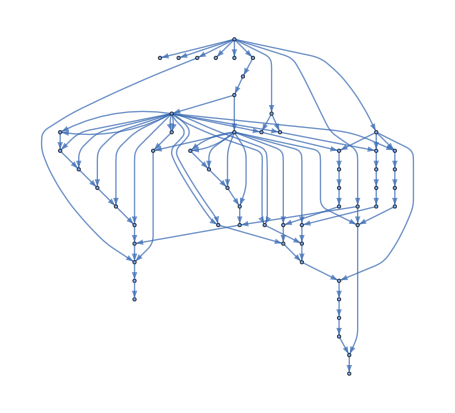

```mathematica
ratFunccmat // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally the output is reconstructed as usual with

```mathematica
ratFuncResult = ReconstructTargetCompanionMatrix[ratFunccmat];
ratFuncResult // Collect[#,{x,y},Factor]&
```

Generated 20 sample points

Approximate time per evaluation (single core): 1.1e-05 sec.

Generated 20 sample points

Approximate time per evaluation (single core): 1e-05 sec.

-((-27934368000-61047574784 a-54369569760 a^2-25113305072 a^3-6352725849 a^4-854413450 a^5-53804282 a^6-1086999 a^7+10974 a^8)/(24880+25688 a+7571 a^2+451 a^3+a^4)^2)+((-20201480960-40653889536 a-36166472096 a^2-17900355312 a^3-5148677755 a^4-813853223 a^5-54325143 a^6-708114 a^7+35484 a^8) y)/(24880+25688 a+7571 a^2+451 a^3+a^4)^2+((58769210880+108331397888 a+78627302208 a^2+20834044928 a^3-3761837826 a^4-3255847679 a^5-616192192 a^6-44350818 a^7-930735 a^8+11046 a^9) y^2)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)-((10097592320-27819160320 a-88517951488 a^2-92415688608 a^3-48235698488 a^4-13067454835 a^5-1716098481 a^6-98929311 a^7-1490046 a^8+35046 a^9) y^3)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)+(a (-29384605440-65408368384 a-61601574688 a^2-30343497664 a^3-7896692159 a^4-1003233493 a^5-55815959 a^6-756830 a^7+21938 a^8) y^4)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)-(a (-5048796160-11337548800 a-10690409344 a^2-5247189584 a^3-1357444684 a^4-171022025 a^5-9396845 a^6-121081 a^7+3882 a^8) y^5)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)

Mathematica does not support multivariate polynomial division of rational functions. However, it is at least possible to check that the result is correct with the following code

```mathematica
PolynomialReduce[ratFuncResult*(ratFunc//Together//Denominator),gb,variables][[2]]//Factor;
PolynomialReduce[(ratFunc//Together//Numerator),gb,variables][[2]]//Factor;
%==%%//Factor
```

True

## Elimination Theory

## List of Examples

## Benchmarks

Related Guides

SPQR

Related Tech Notes

## Metadata

### Categorization

Tech Note

SPQR

SPQR`

SPQR/tutorial/IntroductiontoSPQR

### Keywords